```mathematica
(*Legendre associated polynomial function*)
LGP[j_,m_,θ_]:=Sqrt[(2 j+1)/(4π)((j-m)!)/((j+m)!)] LegendreP[j,m,Cos[θ]]

(*Clebsh-Gordan function*)
CG[j_,m_,J_,M_]:=If[Abs[M-m]<=j&&Abs[M]<=J,ClebschGordan[{j,m},{j,M-m},{J,M}],0]

(*Ladder operators*)
Cplus[j_,m_]  :=√(j( j+1) - m(m+1))
Cminus[j_,m_]:=√(j( j+1) - m(m-1))


(*φ integral when O=Subscript[Z, 1] Subscript[Z, 2]*)
IntZZ[m_, n_] := Module[{numerator,denominator, result},
If [m==n, result = 0,

(*otherwise, if m≠n*)
numerator = ⅈ (-1+ⅇ^(ⅈ (-m+n)π/2))^3 (1+ⅇ^(ⅈ (-m+n)π/2));
denominator = m-n;

result = numerator/denominator];

result // Chop
]

(*φ integral when O=Subscript[X, 1] Subscript[X, 2]*)
IntXX[m_,n_]:=Module[{numerator,denominator,result},
If[m==n,result=1/2 ⅇ^(-3/2 ⅈ m π) (1+ⅇ^(ⅈ m π)+ⅇ^(2 ⅈ m π)+ⅇ^(3 ⅈ m π)) π,

(*otherwise, if m≠n*)
result=-1/(m-n)ⅈ ⅇ^(-2 ⅈ m π) (ⅇ^((ⅈ m π)/2)-ⅇ^((ⅈ n π)/2)+ⅇ^(1/2 ⅈ (2 m+n) π)-ⅇ^(1/2 ⅈ (m+2 n) π)+ⅇ^(1/2 ⅈ (3 m+2 n) π)-ⅇ^(1/2 ⅈ (2 m+3 n) π)+ⅇ^(1/2 ⅈ (4 m+3 n) π)-ⅇ^(1/2 ⅈ (3 m+4 n) π));
];

result // Chop
]
```

```mathematica
Integral[j_,m_,n_]:=Module[{integralPhi,integralTheta,result},
(*Check initial conditions:if |m|>j or |n|>j,return 0*)
If[Abs[m]>j||Abs[n]>j,Return[0]];

integralPhi=IntXX[m,n];
If[integralPhi==0,
result=0,
integralTheta=NIntegrate[LGP[j,m,θ]*LGP[j,n,θ]*Sin[θ],{θ,0,π}];
result=Chop[integralPhi*integralTheta]];
Return[result]
]


IntegralApprox[j_,m_,n_]:=Module[{integralPhi,integralTheta,result},

If[Abs[m]>j||Abs[n]>j,Return[0]];

If[n=!=m&&n=!=m+1&&n=!=m-1&&n=!=m+2&&n=!=m-2,Return[0]];

integralPhi=IntXX[m,n];

If[integralPhi==0,result=0,
integralTheta=NIntegrate[LGP[j,m,θ]*LGP[j,n,θ]*Sin[θ],{θ,0,π}];
result=Chop[integralPhi*integralTheta]];
Return[result]
]
```

```mathematica
(*Subscript[Tr, J][Subscript[A, x]] function with summation all over n, m*)
TrAxComplete[j_,J_]:=Module[{sumM,result,cgm1,cgm2,term},
If[J>2*j,Return[0]];

sumM=Sum[
cgm1=CG[j,m,J,M-m];
cgm2=CG[j,n,J,M-n];

If[cgm1!=0&&cgm2!=0,
term=Cplus[j,m]*Integral[j,m+1,n]+Cminus[j,m]*Integral[j,m-1,n]-Cplus[j,n]*Integral[j,m,n+1]-Cminus[j,n]*Integral[j,m,n-1];

If[term!=0,cgm1*cgm2*term*(Cplus[j,M-m]*Integral[j,M-m+1,M-n]+Cminus[j,M-m]*Integral[j,M-m-1,M-n]-Cplus[j,M-n]*Integral[j,M-m,M-n+1]-Cminus[j,M-n]*Integral[j,M-m,M-n-1]),
0],
0],
{m,-j,j},{n,-j,j},{M,-J,J}];

result=(1/4)*sumM;
Chop[result]]
```

```mathematica
(*Subscript[Tr, J][Subscript[A, x]] function with summation over n=m, n=m+1, n=m-1*)
TrAxApprox[j_,J_]:=Module[{sumM,result,cgm1,cgm2,term},
If[J>2*j,Return[0]];

sumM=Sum[
cgm1=CG[j,m,J,M-m];
cgm2=CG[j,n,J,M-n];

If[cgm1!=0&&cgm2!=0,
term=Cplus[j,m]*IntegralApprox[j,m+1,n]+Cminus[j,m]*IntegralApprox[j,m-1,n]-Cplus[j,n]*IntegralApprox[j,m,n+1]-Cminus[j,n]*IntegralApprox[j,m,n-1];

If[term!=0,cgm1*cgm2*term*(Cplus[j,M-m]*IntegralApprox[j,M-m+1,M-n]+Cminus[j,M-m]*IntegralApprox[j,M-m-1,M-n]-Cplus[j,M-n]*IntegralApprox[j,M-m,M-n+1]-Cminus[j,M-n]*IntegralApprox[j,M-m,M-n-1]),
0],
0],
{m,-j,j},{n,-j,j},{M,-J,J}];

result=(1/4)*sumM;
Chop[result]]





(*Subscript[Tr, J][Subscript[A, z]] function with summation all over n, m*)
TrAzComplete[j_,J_]:=Module[{result,cgm1,cgm2,integral1, integral2},
result=Sum[
cgm1=CG[j,m,J,M-m];
cgm2=CG[j,n,J,M-n];

If[cgm1!=0&&cgm2!=0&&m≠n,-cgm1*cgm2*(m-n)^2*Integral[j,m,n]*Integral[j,M-m,M-n],0],

{m,-j,j},{n,-j,j},{M,-J,J}
];

Chop[result]
]

(*Subscript[Tr, J][Subscript[A, z]] function with summation all over n, m*)
TrAzApprox[j_,J_]:=Module[{result,cgm1,cgm2,integral1, integral2},
result=Sum[
cgm1=CG[j,m,J,M-m];
cgm2=CG[j,n,J,M-n];

If[cgm1!=0&&cgm2!=0&&m≠n,-cgm1*cgm2*(m-n)^2*IntegralApprox[j,m,n]*IntegralApprox[j,M-m,M-n],0],

{m,-j,j},{n,-j,j},{M,-J,J}
];

Chop[result]
]
```

j = 8, J = JJ, TrApprox   = 0
j = 8, J = JJ, TrApprox   = 5.09687
j = 8, J = JJ, TrApprox   = -10.0331
j = 8, J = JJ, TrApprox   = 5.24883
j = 8, J = JJ, TrApprox   = -8.42906
j = 8, J = JJ, TrApprox   = -1.51888
j = 8, J = JJ, TrApprox   = -10.6073
j = 8, J = JJ, TrApprox   = 0.255618
j = 8, J = JJ, TrApprox   = -18.891
j = 8, J = JJ, TrApprox   = -31.7614
j = 8, J = JJ, TrApprox   = 1.42592
j = 8, J = JJ, TrApprox   = 4.47596
j = 8, J = JJ, TrApprox   = -11.2674
j = 8, J = JJ, TrApprox   = 28.4305
j = 8, J = JJ, TrApprox   = 14.4609
j = 8, J = JJ, TrApprox   = -3.26182
j = 8, J = JJ, TrApprox   = -1.22728

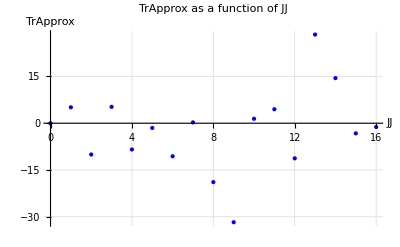

j = 10, J = JJ, TrComplete = 0
j = 10, J = JJ, TrApprox   = 0
j = 10, J = JJ, TrComplete = 5.21738
j = 10, J = JJ, TrApprox   = 5.21738
j = 10, J = JJ, TrComplete = -12.2452
j = 10, J = JJ, TrApprox   = -12.2452
j = 10, J = JJ, TrComplete = -7.20354
j = 10, J = JJ, TrApprox   = -7.25328
j = 10, J = JJ, TrComplete = -17.545
j = 10, J = JJ, TrApprox   = -17.4018
j = 10, J = JJ, TrComplete = -5.39013

j = 10, J = JJ, TrApprox   = -5.65873
j = 10, J = JJ, TrComplete = 21.3082
j = 10, J = JJ, TrApprox   = 21.8058
j = 10, J = JJ, TrComplete = 60.2484
j = 10, J = JJ, TrApprox   = 59.5815
j = 10, J = JJ, TrComplete = -23.2421
j = 10, J = JJ, TrApprox   = -22.5089
j = 10, J = JJ, TrComplete = -29.8939
j = 10, J = JJ, TrApprox   = -30.6365
j = 10, J = JJ, TrComplete = 50.6293
j = 10, J = JJ, TrApprox   = 51.3556
j = 10, J = JJ, TrComplete = 28.6844
j = 10, J = JJ, TrApprox   = 27.9839
j = 10, J = JJ, TrComplete = -20.1089
j = 10, J = JJ, TrApprox   = -19.4009
j = 10, J = JJ, TrComplete = 15.5026
j = 10, J = JJ, TrApprox   = 14.7005
j = 10, J = JJ, TrComplete = -5.8044
j = 10, J = JJ, TrApprox   = -4.85223
j = 10, J = JJ, TrComplete = 4.84978
j = 10, J = JJ, TrApprox   = 3.84011
j = 10, J = JJ, TrComplete = -21.642
j = 10, J = JJ, TrApprox   = -20.7856
j = 10, J = JJ, TrComplete = -26.4178
j = 10, J = JJ, TrApprox   = -26.959
j = 10, J = JJ, TrComplete = -27.8169
j = 10, J = JJ, TrApprox   = -27.5821
j = 10, J = JJ, TrComplete = 37.3553
j = 10, J = JJ, TrApprox   = 37.2939
j = 10, J = JJ, TrComplete = -8.39869
j = 10, J = JJ, TrApprox   = -8.39148

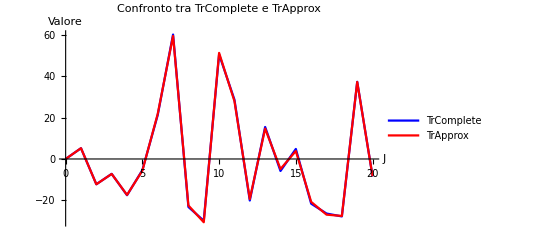

```mathematica
(*Supponiamo che queste funzioni siano già definite*)(*TrAxComplete[jj_,JJ_] e TrAxApprox[jj_,JJ_]*)(*Imposta i valori di j e JJ*)
nQubs=5;
jj=2^(nQubs-1);

(*Calcola i valori di TrComplete e TrApprox per tutti i JJ da 0 a 2*jj*)
JJValues=Range[0,2*jj];
(*TrCompleteValues=Table[TrAzComplete[jj,JJ],{JJ,JJValues}];*)
TrApproxValues=Table[TrAxApprox[jj,JJ],{JJ,JJValues}];

(*Stampa i risultati per j e JJ*)
Do[Print["j = ",jj,", J = ",JJ,", TrApprox   = ",TrApproxValues[[i]]];,{i,Length[JJValues]}];

(*Crea il grafico di TrApprox in base a JJ*)ListPlot[Transpose[{JJValues,TrApproxValues}],PlotStyle->{Blue,PointSize[Medium]},AxesLabel->{"JJ","TrApprox"},PlotLabel->"TrApprox as a function of JJ",GridLines->Automatic]
```

```mathematica
"j = "5", J = "3", TrComplete = "8.699297565559185
"j = "5", J = "3", TrReduced  = "7.221866847278418(tenendo m\pm 1)
"j = "5", J = "3", TrReduced  = "7.221866847278418 (tenendo m\pm 2)
```

```mathematica
Do[
TrReduced=TrAzComplete[jj,JJ];

Print["j = ",jj,", J = ",JJ, ", TrReduced = ",TrReduced],


{jj,jjVals}]
```

j = 5, J = 6, TrComplete = 0

j = 5, J = 6, TrApprox   = 0

j = 5, J = 6, TrComplete = 4.73057

j = 5, J = 6, TrApprox   = 4.73057

j = 5, J = 6, TrComplete = -4.39974

j = 5, J = 6, TrApprox   = -4.39974

j = 5, J = 6, TrComplete = 8.6993

j = 5, J = 6, TrApprox   = 8.62372

j = 5, J = 6, TrComplete = -13.9039

j = 5, J = 6, TrApprox   = -13.6959

j = 5, J = 6, TrComplete = 7.58369

j = 5, J = 6, TrApprox   = 7.29198

j = 5, J = 6, TrComplete = 7.65334

j = 5, J = 6, TrApprox   = 7.90185

j = 5, J = 6, TrComplete = 1.70501

j = 5, J = 6, TrApprox   = 1.5698

j = 5, J = 6, TrComplete = -15.7157

j = 5, J = 6, TrApprox   = -15.6693

j = 5, J = 6, TrComplete = 6.50921

j = 5, J = 6, TrApprox   = 6.50002

j = 5, J = 6, TrComplete = 0.54524

j = 5, J = 6, TrApprox   = 0.546047

```mathematica
"j = "8", J = "JJ", TrApprox   = "0
"j = "8", J = "JJ", TrApprox   = "5.096868524935364
"j = "8", J = "JJ", TrApprox   = "-10.033107927182726
"j = "8", J = "JJ", TrApprox   = "5.248831021197041
"j = "8", J = "JJ", TrApprox   = "-8.429059187544793
"j = "8", J = "JJ", TrApprox   = "-1.5188788148047925
"j = "8", J = "JJ", TrApprox   = "-10.60725527995613
"j = "8", J = "JJ", TrApprox   = "0.2556181780288611
"j = "8", J = "JJ", TrApprox   = "-18.890977396081468
"j = "8", J = "JJ", TrApprox   = "-31.761445646809594
"j = "8", J = "JJ", TrApprox   = "1.4259230590499705
"j = "8", J = "JJ", TrApprox   = "4.475957123842339
"j = "8", J = "JJ", TrApprox   = "-11.26736022285578
"j = "8", J = "JJ", TrApprox   = "28.430501622581893
"j = "8", J = "JJ", TrApprox   = "14.460865262438558
"j = "8", J = "JJ", TrApprox   = "-3.2618194762422936
"j = "8", J = "JJ", TrApprox   = "-1.2272825261750204
```